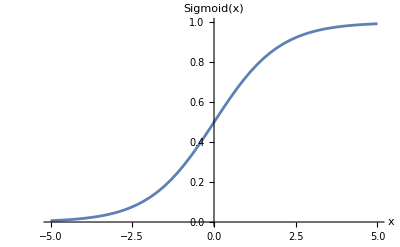

```mathematica
Sigmoid[x_]:=1/(1+Exp[-x])
Plot[Sigmoid[x],{x,-5,5},AxesLabel->{"x","Sigmoid(x)"},PlotRange->{0,1}]
```

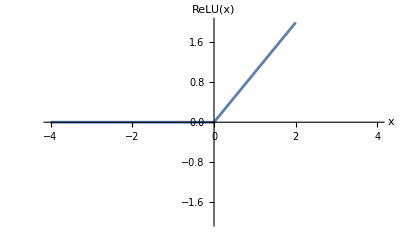

```mathematica
Plot[Max[0,x],{x,-4,4},AxesLabel->{"x","ReLU(x)"},PlotRange->{-2,2}]
```

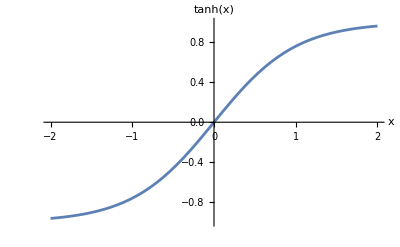

```mathematica
Plot[Tanh[x],{x,-2,2},AxesLabel->{"x","tanh(x)"},PlotRange->{-1,1}]
```

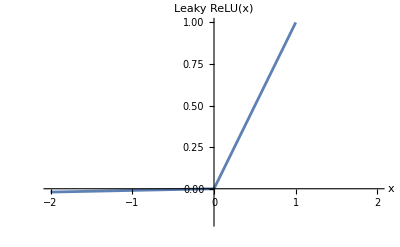

```mathematica
Plot[Piecewise[{{x,x>0},{0.01 x,x<=0}}],{x,-2,2},AxesLabel->{"x","Leaky ReLU(x)"},PlotRange->{-0.2,1}]
```

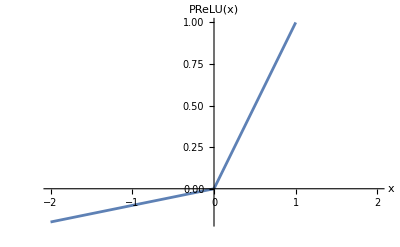

```mathematica
alpha=0.1;  (*You can adjust the alpha value as needed*)
Plot[Piecewise[{{x,x>0},{alpha x,x<=0}}],{x,-2,2},AxesLabel->{"x","PReLU(x)"},PlotRange->{-0.2,1}]
```

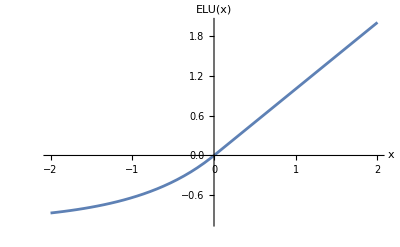

```mathematica
alpha=1;  (*You can adjust the alpha value as needed*)
Plot[Piecewise[{{x,x>0},{alpha (Exp[x]-1),x<=0}}],{x,-2,2},AxesLabel->{"x","ELU(x)"},PlotRange->{-1,2}]
```

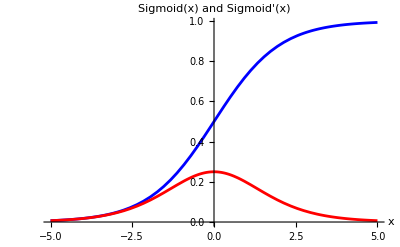

```mathematica
Sigmoid[x_]:=1/(1+Exp[-x])
SigmoidDerivative[x_]:=Sigmoid[x] (1-Sigmoid[x])

Plot[{Sigmoid[x],SigmoidDerivative[x]},{x,-5,5},PlotStyle->{Blue,Red},AxesLabel->{"x","Sigmoid(x) and Sigmoid'(x)"},PlotRange->{Automatic,Automatic}]
```

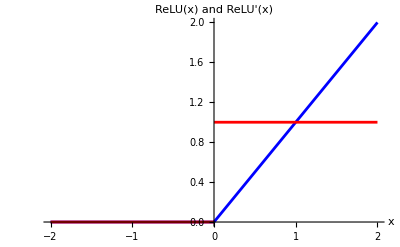

```mathematica
ReLU[x_]:=Max[0,x]
ReLUDerivative[x_]:=Piecewise[{{1,x>0},{0,x<=0}}]

Plot[{ReLU[x],ReLUDerivative[x]},{x,-2,2},PlotStyle->{Blue,Red},AxesLabel->{"x","ReLU(x) and ReLU'(x)"},PlotRange->{Automatic,Automatic}]
```

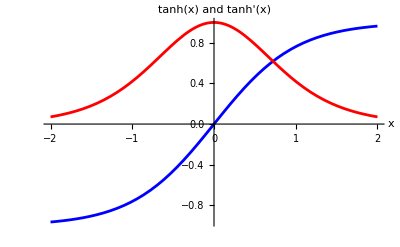

```mathematica
TanhDerivative[x_]:=1-Tanh[x]^2

Plot[{Tanh[x],TanhDerivative[x]},{x,-2,2},PlotStyle->{Blue,Red},AxesLabel->{"x","tanh(x) and tanh'(x)"},PlotRange->{Automatic,Automatic}]
```

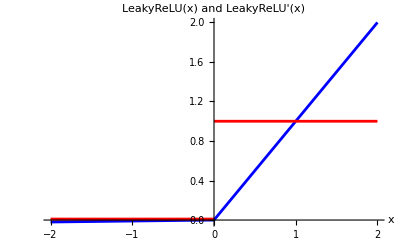

```mathematica
LeakyReLU[x_,alpha_]:=Piecewise[{{x,x>0},{alpha x,x<=0}}]
LeakyReLUDerivative[x_,alpha_]:=Piecewise[{{1,x>0},{alpha,x<=0}}]

alpha=0.01;  (*You can adjust the alpha value as needed*)
Plot[{LeakyReLU[x,alpha],LeakyReLUDerivative[x,alpha]},{x,-2,2},PlotStyle->{Blue,Red},AxesLabel->{"x","LeakyReLU(x) and LeakyReLU'(x)"},PlotRange->{Automatic,Automatic}]
```

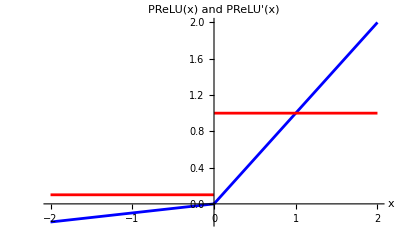

```mathematica
PReLU[x_,alpha_]:=Piecewise[{{x,x>0},{alpha x,x<=0}}]
PReLUDerivative[x_,alpha_]:=Piecewise[{{1,x>0},{alpha,x<=0}}]

alpha=0.1;  (*You can adjust the alpha value as needed*)
Plot[{PReLU[x,alpha],PReLUDerivative[x,alpha]},{x,-2,2},PlotStyle->{Blue,Red},AxesLabel->{"x","PReLU(x) and PReLU'(x)"},PlotRange->{Automatic,Automatic}]
```

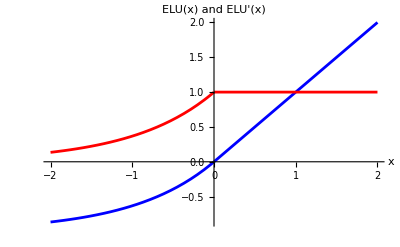

```mathematica
ELU[x_,alpha_]:=Piecewise[{{x,x>0},{alpha (Exp[x]-1),x<=0}}]
ELUDerivative[x_,alpha_]:=Piecewise[{{1,x>0},{ELU[x,alpha]+alpha,x<=0}}]

alpha=1;  (*You can adjust the alpha value as needed*)
Plot[{ELU[x,alpha],ELUDerivative[x,alpha]},{x,-2,2},PlotStyle->{Blue,Red},AxesLabel->{"x","ELU(x) and ELU'(x)"},PlotRange->{Automatic,Automatic}]
```